# Hemispherical Sampling - Notes and Derivations

-Graphics--Graphics-

Brief trigo recap : 

On a unit sphere the radius is 1. So we don’t use it in practice.
Theta θ range is (r)π/2 (ie. 90° or a quarter circumference). 
Phi ϕ range is (r)2π (ie. 360° or the full circle circumference).

Sinθ works for our tiny ⅆω area calculation because theta is on the opposite of the right triangle compared to the side we’re calculating. So that : 
Sinθ = opposite/hypotenuse but because the hypotenuse is the radius which is 1 .. Sinθ is the opposite side .. Sinθ = opposite/1 = opposite.
Intuitively the ‘parallel’ radii are shrinking while getting closer to the poles (while radii around ϕ are not) 

Note that the ususal Theta θ goes from the xy plane and up while here goes down from the normal so the resulting point (coord) on the sphere is called co-latitude.

Keep in mind that Cosθ is not only the x coord (adjacent side) in a circle setup but really because of that is the vector projection of a vector pointing on the hemisphere onto the direction of N (above, it’s the vector pointing up), ie. it is F.N (Dot[F,N]) aka the scalar projection of F onto the directions of N. So actually Cosθ accounts for the projected surface area in a hemispherical radiance setup.. ie. the projected solid angle measure is related to the solid angle measure by : 

ⅆ ω^⊥ = |Cosθ|ⅆω

-Graphics-

So the irradiance integral is : ∫_Ω L_o(p,ω)cosθⅆωⅆΑ = ∫_Ω L_o(p,ω)ⅆ ω^⊥ⅆΑ = ∫_0^(2π) ∫_0^π L_i(p,θ,ϕ) cosθ sinθ ⅆθⅆϕ

Eventually, differential area is related to differential solid angle (as viewed from a point ) by :

ⅆω = ⅆΑcosθ/r^2

-Graphics-

See this for the full derivation : https://math.stackexchange.com/questions/3072622/derivation-of-frac-cos-thetadar2-d-omega?rq=1

Intuitively, on a unit sphere (r=1), ⅆΑcosθ = ⅆω and if it is perpendicularly aligned with ⅆω then θ=0 and cosθ=1 so ⅆΑ=ⅆω. 
Then if ⅆΑ starts getting far away or rotating away from the perp⊥ vector .. r^2 and cosθ terms will compensate accordling to reduce ⅆω. 

-Graphics-

Therefore, we can write the irradiance integral as :

∫ Lcosθ_i(cosθ_o ⅆΑ)/r^2

-Graphics-

-Graphics-

-Graphics-


-Graphics-

Take care radiant flux contains also a 4π  because the flux energy flows through a surface equal to the surface area A of a sphere with a radius of r metres.

Ε = Φ/A= (4π Φ)/(4π r^2)= Φ/r^2

----------------------------------------------------------------------------------------------------------------
Let’s recap radiometric/photometric quantities : 

-> radiant flux (luminous flux) : change of luminous energy with time

Φ = (ⅆ Ϟ_t)/ⅆt

we can compute the total light hitting a surface up to time τ as : 
Q_t=∫_0^t Φ_t ⅆt
flux is in watts(W) where watt is one Joule per second (so a 50watt light bulb draws 50J of energy per second).

-> radiant intensity (luminous intensity) : density of luminous flux with respect to solid angle in a specified direction 

I_v= ⅆΦ_v/ⅆΩ

the distribution of the luminous intensities as a function of the direction of emission is used to determine the luminous flux within a certain solid angle:
Φ_v = ∫∫_Ω I_v(θ,ϕ) sinθ ⅆθⅆϕ

-> radiance (luminance) : density of luminous intensity with respect to projected area in a specified direction at a specified point on a surface

L_v=(ⅆ I_v)/ⅆA1/cosθ 

Radiance is a measure of the rate at which light energy is emitted from a surface in a particular direction.
It is a function of position and direction, and it is often denoted by L.
Formally, it is defined as power per steradian per surface area (W ·sr^-1· m^-2).

-Graphics-

The definition of luminance can be thought of as dividing a surface into an infinite number of infinitesimally small surfaces, 
which can be considered as point sources, each of which has a specific luminous intensity, Iv, in the specified direction. 
The luminance of the surface is then the integral of these luminance elements over the whole surface.
We know from above that sometimes we prefer to have a ⅆΩ (diffferential solid angle) instead of differential area.

-> irradiance (illuminance) : density of incident luminous flux with respect to area at a point on a surface

Ε_v=(ⅆ Φ_v)/ⅆA


The lumen (lm) is the photometric equivalent of the watt, weighted to match the eye response of the “standard observer”.

-Graphics-

-Graphics-

----------------------------------------------------------------------------------------------------------------
Solid angle and angular extents

In 2D, angular extent is just the angle between two directions, and we normally specify angular extent in radians. 
The angular extent between two rays emanating from a point q ̄ can be measured using a circle centered at q ̄; 
that is, the angular extent (in radians) is just the circular arc length l of the circle between the two directions, divided by radius r of the circle, l/r.

-Graphics-

In 3D, the quantity corresponding to 2D angular extent is called solid angle.
Solid angle is measured as the area a of a patch on a sphere, divided by the squared radius of the sphere.

ω = α/r^2

-Graphics-

The unit of measure for solid angle is the steradian (sr). A solid angle of 2π steradians corresponds
to a hemisphere of directions. The entire sphere has a solid angle of 4π sr.
Note that the solid angle of a patch does not depend on the radius r, since the projected area a is proportional to r^2.

To compute the solid angle of a patch on the surface of a sphere we just integrate the differential solid angle over
the patch region on a unit sphere :

∫_ϕ0^ϕ1 ∫_θ0^θ1 Sin[θ]ⅆθⅆϕ  = (ϕ1-ϕ0) (Cos[θ0]-Cos[θ1])

----------------------------------------------------------------------------------------------------------------

```mathematica
(* as seen above .. when we're integrating in spherical coordinates ... the differential solid angle ⅆω is not just ⅆθⅆϕ but Sin[θ]ⅆθⅆϕ .. from the geometrical intuition with basic trigonometry ⅆω is in spherical coords Sin[θ]ⅆθⅆϕ .. because one side is ⅆϕ and the other Sin[θ]ⅆθ .. ie. it is the product of the differential lengths of its sides *)

(* we can also use the 'Jacobian' to see if Sin[θ] comes up in the transformation from cartesian to spherical *)
Clear[r,θ,ϕ]; (* custom fnc for the JacobianDet(erminat) as with former VectorAnalysis module*)
JacobianDet[f_List,vars_List]:=Simplify[Det[Outer[D,f,vars]]]
{D[FromSphericalCoordinates[{r,θ,φ}],{{r,θ,φ}}]//MatrixForm,"→ Jacobian Matrix"}
{JacobianDet[FromSphericalCoordinates[{r,θ,φ}],{r,θ,φ}],"→Jacobian Determinant"}


(* let's see if Sin[θ] is effective .. ie. if we integrate over theta and phi we should get the unit sphere area .. which is 4π *)

Clear[t,p,θ,ϕ,Ω];

∫_0^Ω ⅆω;                                (* integral with differential area/solidangle ⅆω *)

∫_0^(2π) ∫_0^π ⅆθⅆϕ                    (* not correct, integration result is not surface sphere area *)
∫_0^(2π) ∫_0^π Sin[θ]ⅆθⅆϕ      (* correct, integral in spherical coordinates *)


(* same for projected solid angles *)
ⅆΩ = Sin[θ]ⅆθⅆϕ;
ⅆ Subscript[Ω, proj]=Cos[θ]ⅆΩ;
Subscript[Ω, proj]=∫_0^(2π) ∫_0^α Cos[θ]Sin[θ]ⅆθⅆϕ 
Subscript[Ω, proj] =π Sin[α]^2;

(* calculate solid angle for a patch of sides ϕ1-ϕ0 * θ1-θ0 *)
∫_ϕ0^ϕ1 ∫_θ0^θ1 Sin[θ]ⅆθⅆϕ
```

{(Cos[φ] Sin[θ] | r Cos[θ] Cos[φ] | -r Sin[θ] Sin[φ]
Sin[θ] Sin[φ] | r Cos[θ] Sin[φ] | r Cos[φ] Sin[θ]
Cos[θ] | -r Sin[θ] | 0),→ Jacobian Matrix}

{r^2 Sin[θ],→Jacobian Determinant}

2 π^2

4 π

π Sin[α]^2

(-ϕ0+ϕ1) (Cos[θ0]-Cos[θ1])

```mathematica
(* THIS NEEDS TO BE EVALUATED FOR ALL THE REMAINING TO WORK !!! *)

Clear[hemisphere,sp,r,θ,ϕ];

(* use revolution to draw an hemisphere *)
hemisphere=First@RevolutionPlot3D[Sqrt[1-r^2],{r,0,1},Mesh->None,PlotStyle->{RGBColor[0.59,0.77,0.75],Opacity[0.25]}];

(* let's see how VM is mapping sp->cart *)
CoordinateTransformData["Spherical"->"Cartesian","Mapping", {r,θ,ϕ}]
FromSphericalCoordinates[{r,θ,φ}]

(* use that to manually convert from spherical to cartesian coordinates *)
(*sp[{r_,theta_,phi_}]:=r {Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]};*)
sp[{r_,theta_,phi_}]:=r {Cos[phi]Sin[theta],Sin[theta] Sin[phi],Cos[theta]};

(* THIS NEEDS TO BE EVALUATED FOR ALL THE REMAINING TO WORK !!! *)
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

{r Cos[φ] Sin[θ],r Sin[θ] Sin[φ],r Cos[θ]}

----------------------------------------------------------------------------------------------------------------

```mathematica
(* Uniform and Cosine Weighted Hemispherical Sampling *)

Clear[ϕ,θ,p,t,margd,cond,cdfmargd,cdfcond];

∫_0^Ω ⅆω; (* density function defined over solid angle Ω *)
∫_0^(2π) ∫_0^(π/2) Sin[t]ⅆtⅆp (* hemispherical integral in spherical coords *)
∫_0^(2π) ∫_0^(π/2) 1/(2π)Sin[t]ⅆtⅆp (* PDF for hemispherical integral in spherical coords, note: it's a constant *)


∫_0^Ω Cos[t]ⅆω; (* density function defined over solid angle Ω *)
∫_0^(2π) ∫_0^(π/2) Cos[t]Sin[t]ⅆtⅆp (* cosine weighted hemispherical integral in spherical coords *)
∫_0^(2π) ∫_0^(π/2) Cos[t]/π Sin[t]ⅆtⅆp  (* PDF for cosine weighted hemispherical integral in spherical coords *)


margd=∫_0^(2π) Cos[t]/π Sin[t]ⅆp (* Theta marginal density *)
cond=(Cos[t]/π Sin[t])/(2 Cos[t] Sin[t])      (* Phi conditional density *)


cdfmargd=∫_0^t margdⅆt (* CDF for theta PDF *)
cdfcond=∫_0^p condⅆp (* CDF for phi PDF *)


Solve[cdfmargd==ξ,t] (* sampling fnc for theta *)
Solve[cdfcond==ξ,p] (* sampling fnc for phi *)


(* Cosine Weighted - Sampling functions in spherical coords *)
samplecoshemiphi[x_] =2π*x ;
samplecoshemitheta[x_]=ArcSin[√x];

(* Cosine Weighted - Sampling functions in cartesian coords *)
Clear[θ,ϕ];

ϕ =2π*Subscript[ξ, 1] ;
θ=ArcSin[√Subscript[ξ, 2]];
CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,θ,ϕ}]
```

2 π

1

π

1

2 Cos[t] Sin[t]

1/(2 π)

Sin[t]^2

p/(2 π)

{{t→ConditionalExpression[-ArcSin[√ξ]+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[π-ArcSin[√ξ]+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[ArcSin[√ξ]+2 π C[1], C[1]∈ℤ]},{t→ConditionalExpression[π+ArcSin[√ξ]+2 π C[1], C[1]∈ℤ]}}

{{p→2 π ξ}}

{Cos[2 π ξ_1] √ξ_2,Sin[2 π ξ_1] √ξ_2,√(1-ξ_2)}

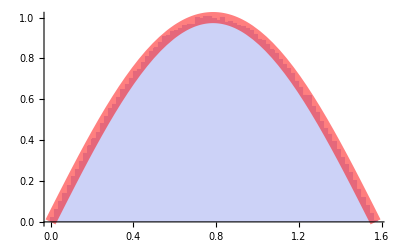

```mathematica
(* let's see if our sampling fnc matches the PDF *)
Clear[n, totsamples];

n=10;
totsamples = 10^6;
sampleHemiDis:=ArcSin[√#]&[RandomReal[]]

Show[
Histogram[ParallelTable[sampleHemiDis,{i,Range[totsamples]}],64,"PDF",PlotTheme->"Classic"],
Plot[2π Cos[t]/π Sin[t],{t,0,π/2},PlotStyle->Directive[Red,Thickness[0.02],Opacity[0.5]]]
]
(* note the added 2π in the Plot[] as domain is hemispherical where with an isotropic NDF .. sampling around Phiϕ is rotationally invariant as seen both in the intro and in the derivation of the sampling routines *)

(* it's easy to see that with our sampling routine we're effectively filling the area under the curve defined by our PDF *)
```

```mathematica
Clear[x,y,z,θ,ϕ]

(ir=ImplicitRegion[z>0&&x^2+y^2+z^2==1,{x,y,z}])//DiscretizeRegion//RegionPlot3D
Integrate[{0,0,1}.{x,y,z},{x,y,z}∈ir] (* define an hemisphere and integrate over it *)


(* let's note that the integral of the cosine hemisphere is half the hemisphere area *)

(* while the integral of the full hemisphere is the hemisphere area 2π *)
(* which also means that for any direction we shall divide by 2π *)
(* which can be seen as the full range of directions we may take on *)

(* compared with the cosine, this means that on the same density of directions we have less directions to spawn *)
(* or that on the same number of directions we will get densier (closer to the true value estimations) *)
(* or also that we'll get more important directions because ie. approaching theta = π/2 cos approaches zero *)

Integrate[Cos[θ] Sin[θ],{θ,0,Pi/2},{ϕ,0,2 Pi}]
Integrate[Sin[θ],{θ,0,Pi/2},{ϕ,0,2 Pi}]
```

-Graphics3D-

π

π

2 π

```mathematica
(* visualize cosine weighted sampling *)

Clear[g,x,nbpts,ptcolor,rndThetaData,rndPhiData,sph3Ddata,xyz3Ddata,sph2Ddata];

(* Parameters *)
nbpts=3000;
ptcolor = RGBColor[1,0.5,0.5,0.5];

(* Random data *)
rndThetaData = RandomReal[1,nbpts];
rndPhiData=RandomReal[1,nbpts];
sph3Ddata = Thread[{1,samplecoshemitheta[rndThetaData],samplecoshemiphi[rndPhiData]}];
xyz3Ddata=sp/@sph3Ddata; (* convert spherical to cartesian *)

(* PDF *)
hemipdf[t_]=Cos[t]/π ; (* hemispherical cos weighted PDF *)
thetaData = Flatten[sph3Ddata/.{x_,y_,z_}->{y}];
pdfTheta=Map[hemipdf,thetaData];

(* Colors *)
CoolColor[ z_ ] :=RGBColor[z,0,0];
RGBColor[#,0,0]&/@pdfTheta;

fxcolor=ColorData["SunsetColors"]/@pdfTheta (* pre-gen colors *); (* SunsetColors AvocadoColors *)
color[x_]:=ColorData["SolarColors"][x];(*color/@pdfTheta;*)  (* aux: map pdfTheta to color fnc to get pts colors *)

(* Plot points and arrows *)
{Show[Graphics3D[{hemisphere,PointSize[0.06],Point[xyz3Ddata,VertexColors->fxcolor]}],Boxed->False,ImageSize->500],
Show[Graphics3D[Table[Style[Arrow[{{0,0,0},x}],ptcolor],{x,xyz3Ddata}],Boxed->False],ImageSize->500]}

(* Plot 2D phi and theta coords as points on an π/2 ↔ 2π axis *)
sph2Ddata=sph3Ddata/.{x_,y_,z_}->{z,y}; (* remove fixed radius and swap theta with phi *)
ListPlot[sph2Ddata,PlotRange->{{0,2π},{0,π/2}},AxesLabel->{2π,π/2},LabelStyle->Directive[GrayLevel[0.5],Bold],PlotStyle->{ptcolor},ImageSize->750, ColorFunction -> CoolColor]

(* Plot PDF *)
Plot[Cos[t]/π Sin[t],{t,0,π/2},PlotLabels->"Expressions",PlotRange->All]

(* note how fewer samples close to the equator and how sampling from cosTheta/π PDF we have more chances to get dirs closer to the upper hemisphere .. pts are PDF color coded *)
```

{-Graphics3D-,-Graphics3D-}

-Graphics-

-Graphics-

On a side note, let’s also not forget to mention why cosine weighted is so nice .. because the rendering eq has a cos in its formulation .. so cosine sampling is proportional to that and the cos cancels out .. which eventually means that our samples have always a weight of 1 (perfect importance sampling) or of 0 (which is discarted) .. because without multipling by cos(θ) all the samples have a nice weight while with cos(θ) approaching the horizont we would have very low importance being the cos(θ) approaching 0.

----------------------------------------------------------------------------------------------------------------

```mathematica
(* Phong Normalization Factor Derivation *)

Clear[t,p,n];

∫_0^Ω Cos[t]^n ⅆω;

∫_0^(2π) ∫_0^(π/2) Cos[t]^n Sin[t]ⅆtⅆp (* never label the limits ie. t=0 and p=0 just leave the zero or it won't work with WM ! *)
2π∫_0^(π/2) Cos[t]^n Sin[t]ⅆt
(* without WM we could get the above manually with integration by parts .. *)
(* so we know that to have the above as a PDF we need the reciprocal of our result to have the integral equating to 1 *)

∫_0^(2π) ∫_0^(π/2) (1+n)/(2π)Cos[t]^n Sin[t]ⅆtⅆp (* Normalized Phong PDF .. integrates to 1 *)
```

(2 π)/(1+n)

ConditionalExpression[(2 π)/(1+n), Re[n]>-1]

1

```mathematica
(* energy conserving Blinn-Phong *)
Clear[t,p,n];
∫_0^(2π) ∫_0^(π/2) (n+2)/(2π)Cos[t]^n Sin[t]ⅆtⅆp
```

(2+n)/(1+n)

```mathematica
(* because we have two variables, when a variable is considered by itself, its density fnc is called marginal density function, which tells us the probability of that single event to occur, indipendently from the other. So if we have θ and ϕ we first integrate around ϕ to get the PDF of θ *)

Clear[pf,θ,n,t,p,ϕ,x,sϕ,s];

pf=(n+1)/(2π)Cos[θ]^n Sin[θ]; (* PDF for a normalized Phong BRDF with specular power notation in θ and ϕ *)

(* to get the probability of θ, integrate around ϕ *)
Integrate[pf,{ϕ,0,2π}];(* same as below *)
{mdfpf=∫_0^(2π) pfⅆϕ,"→ Thetaθ PDF with marginal density fnc"}
{Assuming[n>-1,∫_0^(π/2) pfⅆθ],"→ Phiϕ PDF with marginal density fnc"}

(* then use marginal density function to get the conditional density function to get the PDF for ϕ *)
{conddf = pf/mdfpf,"→ Phiϕ PDF with conditional density fnc"} (* same as above *)

(* we have now our two indipendent PDFs, let's integrate them to get their respective CDFs *)
{cdfphi=∫_0^sϕ conddfⅆϕ,"→ Phiϕ CDF"} (* note, we integrate from 0 to ϕ so later we'll be able to sample ϕ *)
(*cdftheta=∫_0^sθ (1+n) Cos^n[θ] Sin[θ]ⅆθ;*)(* here we have problems with WM .. let's put it in another way *)
𝒟=ProbabilityDistribution[(1+n) Cos[x]^n Sin[x],{x,0,s}]; (* if anything fails .. see https://www.integral-calculator.com/ or https://www.symbolab.com/solver/integral-calculator *)
{Assuming[x>0&&x-s≥0,cdftheta=CDF[𝒟]],"→ Thetaθ CDF"}

(* now let's set our CDFs to a random variable and solve for the sampling variable, ie inverse transform mtd *)
{Solve[cdfphi==ξ,sϕ],"→ Phiϕ Sampling fnc"}
{Solve[1-Cos[sθ]^(1+n)==ξ,sθ],"→ Thetaθ Sampling fnc"}


(* Phong - Sampling functions in spherical coords *)
samplephongphi[x_]=2π*x;
samplephongtheta[x_]=ArcCos[(1-x)^(1/(1+n))];

(* Phong - Sampling functions in cartesian coords *)
Clear[θ,ϕ];

ϕ =2π*Subscript[ξ, 1] ;
θ=ArcCos[(1-Subscript[ξ, 2])^(1/(1+n))];
CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,θ,ϕ}]
```

{(1+n) Cos[θ]^n Sin[θ],→ Thetaθ PDF with marginal density fnc}

{1/(2 π),→ Phiϕ PDF with marginal density fnc}

{1/(2 π),→ Phiϕ PDF with conditional density fnc}

{sϕ/(2 π),→ Phiϕ CDF}

{Function[x,Piecewise[{{1-Cos[s]^(1+n), s>0}, {0, True}}],Listable],→ Thetaθ CDF}

{{{sϕ→2 π ξ}},→ Phiϕ Sampling fnc}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{{sθ→-ArcCos[(1-ξ)^(1/(1+n))]},{sθ→ArcCos[(1-ξ)^(1/(1+n))]}},→ Thetaθ Sampling fnc}

{Cos[2 π ξ_1] √(1-(1-ξ_2)^(2/(1+n))),Sin[2 π ξ_1] √(1-(1-ξ_2)^(2/(1+n))),(1-ξ_2)^(1/(1+n))}

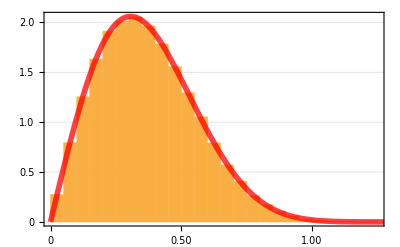

```mathematica
(* let's see if the sampling fnc matches the PDF *)
Clear[n];
n=10;
samplePhongDis:=ArcCos[(1-#)^(1/(1+n))]&[RandomReal[]]
Show[
Histogram[ParallelTable[samplePhongDis,{i,Range[10^5]}],Automatic,"PDF",PlotTheme->"Business"],
Plot[2π(n+1)/(2π)Cos[t]^n Sin[t],{t,0,π/2},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]]]
]
```

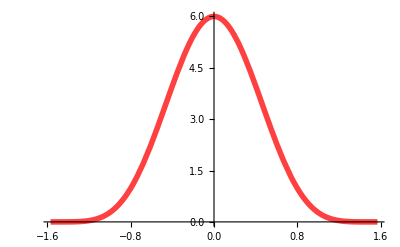

```mathematica
(* because of the sin[t] we ain't getting the real shape of the Phong PDF *)
(* try it with n=1 to see it approaching cosine *)
Clear[n];
n=5;
Plot[2π(n+1)/(2π)Cos[t]^n,{t,-π/2,π/2},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]],PlotRange->All]
```

{-Graphics3D-,-Graphics3D-}

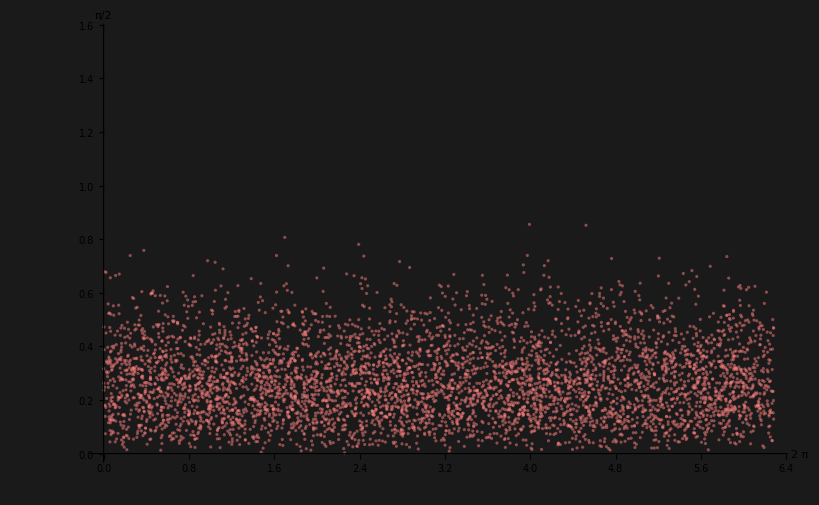

```mathematica
Clear[n,nbpts,ptcolor,gfxsize];

(* Parameters *)
n=20;                                                                            (* Phong exponent; note: with n=1 we end up cosine .. π Cos[θ]Sin[θ] *)
nbpts = 5000;                                                            (* number of points to plot *)
ptcolor = RGBColor[1,0.5,0.5,0.5];        (* points and arrows color *)
gfxsize = 400;                                                          (* size of the plots *)

(* Pre-generate points on the hemisphere and transform to cartesian, for arrows *)
g=sp/@ParallelTable[{1,samplephongtheta[RandomReal[]],samplephongphi[RandomReal[]]},{nbpts/10}];


(* Plot points and arrows *)
{
Show[Graphics3D@{hemisphere,Style[Point[sp/@ParallelTable[{1,samplephongtheta[RandomReal[]],samplephongphi[RandomReal[]]},{nbpts}]],ptcolor]},
Boxed->False,ImageSize->{gfxsize,gfxsize},Background->GrayLevel[0.1]],

Show[
Graphics3D@{hemisphere,Table[Style[Arrow[{{0,0,0},x}],ptcolor],{x,g}]},
Boxed->False,ImageSize->{gfxsize,gfxsize},Background->GrayLevel[0.1]]
}

(* Get random phis and thetas with a Phong distribution and plot them *)
ParallelTable[{samplephongphi[RandomReal[]],samplephongtheta[RandomReal[]]},{nbpts}];
ListPlot[%,PlotRange->{{0,2π},{0,π/2}},AxesLabel->{2π,π/2},LabelStyle->Directive[GrayLevel[0.5],Bold],PlotStyle->{ptcolor},ImageSize->{(gfxsize*2)+(gfxsize/20),(gfxsize*2)-(gfxsize/1.6)},Background->GrayLevel[0.1]]
```

```mathematica
Clear[n,g,x,nbpts,ptcolor,rndThetaData,rndPhiData,sph3Ddata,xyz3Ddata,sph2Ddata];

(* Parameters *)
n=10;                                                                                 (* Phong exponent; note: with n=1 we end up cosine .. π Cos[θ]Sin[θ] *)
nbpts=500;                                                                      (* number of points *)
ptcolor = RGBColor[0.31,0.35,0.22];            (* arrows color *)

(* Random data *)
rndThetaData = RandomReal[1,nbpts];
rndPhiData=RandomReal[1,nbpts];
sph3Ddata = Thread[{1,samplephongtheta[rndThetaData],samplephongphi[rndPhiData]}];
xyz3Ddata=sp/@sph3Ddata; (* convert spherical to cartesian *)

(* PDF *)
phongpdf[t_]=(n+1)/(2π)Cos[t]^n ; (* Phong PDF *)
thetaData = Flatten[sph3Ddata/.{x_,y_,z_}->{y}];
pdfTheta=Map[phongpdf,thetaData];

(* Colors *)
CoolColor[ z_ ] :=RGBColor[z,0,0];
(*RGBColor[#,0,0]&/@pdfTheta*)
fxcolor=ColorData["AvocadoColors"]/@pdfTheta (* pre-gen colors *); (* SunsetColors AvocadoColors *)


(* Plot points and arrows *)
{Show[Graphics3D[{hemisphere,PointSize[0.02],Point[xyz3Ddata,VertexColors->fxcolor]}],
Graphics3D[Table[Style[Arrow[{{0,0,0},x}],ptcolor],{x,xyz3Ddata}]],Boxed->False,ImageSize->300],

(* Plot 2D phi and theta coords as points on an π/2 ↔ 2π axis *)
sph2Ddata=sph3Ddata/.{x_,y_,z_}->{z,y}; (* remove fixed radius and swap theta with phi *)
ListPlot[sph2Ddata,PlotRange->{{0,2π},{0,π/2}},AxesLabel->{2π,π/2},LabelStyle->Directive[GrayLevel[0.5],Bold],PlotStyle->{ptcolor}, ColorFunction -> CoolColor,ImageSize->300],

(* Plot Phong PDF *)
Plot[(n+1)/(2π)Cos[t]^n,{t,0,π/2},PlotLabels->"Expressions",ImageSize->450]}
```

{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
(* Reflect an incoming vector (θ,ϕ) and generate outgoing dirs around that *)
(* TODO : LET'S CUT POINT OUTSIDE HEMISPHERE *)

Clear[normal,n,r,tocart,incoming,outgoing];

(* Helper functions *)
r[n_,d_]=(2*(d.n)*n)-d;                                         (*reflect with projections note the -d to reflect on the xy hemiplane*)
tocart[t_,p_] = sp[{1,t,p}] ;                                   (*convert to cartesian*)
newrotax[t_,p_]:=r[{0,0,1},tocart[t,p]];  (* new axe to rotate around to feed RotationTransform *)

(* Arrows *)
incoming[t_,p_]=Style[Arrow[{tocart[t,p],{0,0,0}}],RGBColor[1,1,0.5,1]];
outgoing[t_,p_]=Style[Arrow[{{0,0,0},r[{0,0,1},tocart[t,p]]}],RGBColor[1,0.5,1,1]];
normal = Style[Arrow[{{0,0,0},{0,0,1}}],RGBColor[0.5,1,0.5,0.5]];


(* Parameters *)
Clear[n,nbpts];
n=50;
nbpts=500;

Manipulate[
Show[
Graphics3D@{
hemisphere,
normal,
incoming[t,p],
outgoing[t,p],Style[Point[RotationTransform[{{0,0,1},newrotax[t,p]}][sp/@ParallelTable[{1,ArcCos[(1-RandomReal[])^(1/(1+n))],samplephongphi[RandomReal[]]},{nbpts}]]],RGBColor[1.0,0.5,0.5]]
},
Boxed->False,ImageSize->450
],
{{t,0.8,"Theta θ"},0.0,Pi/2-0.0,0.1},{{p,1.2,"Phi ϕ"},0.0,2 Pi},{{n,50,"Phong Exp"},1,1000}
]
```

```mathematica
(* To use it above before manipulate for testing purposes *)

(* Hardcoded vector test *)
(*
Clear[iline,d,t,p,reflectRot,reflectDot];
RotationTransform[Pi,{0,0,1}][{1,1,2}];    (*reflect by rotating 180° around normal*)
reflectRot = Style[Arrow[{{0,0,0},RotationTransform[Pi,{0,0,1}][{1,1,2}]}],Red];
reflectDot = Style[Arrow[{{0,0,0},r[{0,0,1},{1,1,2}]}],Blue];
iline= Style[Arrow[{{1,1,2},{0,0,0}}],RGBColor[1,1,0.5,1]];
Show[Graphics3D@hemisphere,Graphics3D@iline,Graphics3D@normal,Graphics3D@reflectRot,Boxed->False]
VectorAngle[{1,1,2},{-1,-1,2}];(*angle between incoming and outgoing vectors*)
*)

(* Random data *)
(*
Clear[rndThetaData,rndPhiData,sph3Ddata,xyz3Ddata,phongpdf,thetaData,pdfTheta];
rndThetaData = RandomReal[1,nbpts];
rndPhiData=RandomReal[1,nbpts];
sph3Ddata = Thread[{1,samplephongtheta[rndThetaData],samplephongphi[rndPhiData]}];
xyz3Ddata=sp/@sph3Ddata; (* convert spherical to cartesian *)
phongpdf[t_]=(n+1)/(2π)Cos[t]^n ; (* Phong PDF *)
thetaData = Flatten[sph3Ddata/.{x_,y_,z_}->{y}];
pdfTheta=Map[phongpdf,thetaData];

fxcolor=ColorData["AvocadoColors"]/@pdfTheta (* pre-gen colors *); (* SunsetColors AvocadoColors *)
*)
```

----------------------------------------------------------------------------------------------------------------

```mathematica
(* GGX microfacet Normal Distribution *)

Clear[GGXNDF,GGXPDF,tPDF,pPDF,n,m,a,t,p,s];

GGXNDF=a^2/(π (1+(a^2-1) Cos[n·m]^2)^2);   (* GGX NDF *)

GGXPDF=(a^2 Cos[t] Sin[t])/(π (1+(a^2-1) Cos[t]^2)^2);        (* GGX PDF *)

∫_0^(2π) ∫_0^(π/2) GGXPDFⅆtⅆp (* check it's a PDF and so integrates to 1 *)


tPDF=∫_0^(2π) GGXPDF ⅆp (* let's get theta PDF with marginal density fnc *)
pPDF =GGXPDF/tPDF (* let's get the remaining phi PDF with conditional density fnc *)
(* of course it's still 1/2π (as for coshemi and phong) because also here we're rotationally invariant on phi *)
(* and so it will be the sampling fnc for phi.. 2πξ *)


(* because marginal and conditional are independent regard which one of the joint probabilities we want to sample with one of them .. marginalizing first phi it should give us the same result we get while using the conditional fnc *)
∫_0^(π/2) GGXPDFⅆt 

(* let's integrate our theta PDF to get its CDF *)
ggxCDF=Integrate[(2 a^2 Cos[t] Sin[t])/((1+(a^2-1) Cos[t]^2)^2),{t,0,s},Assumptions->a>0 && s>0]

(* because all other online derivations give the below result .. let's check they are the same *)
ggxCDFothers = 2 a^2(1/((2 a^4-4 a^2+2)Cos[s]^2+2 a^2-2)-1/(2 a^4-2 a^2));
TrueQ[FullSimplify[ggxCDFothers==ggxCDF]]

(* eventually let's solve for our angle *)
solGGX = Solve[ggxCDF==ξ,s,Reals,Assumptions->a>0 && ξ>0];
Normal[solGGX]; (* removes conditions *)
FullSimplify[%,Assumptions->a>0 && ξ>0]

FullSimplify[Normal[Solve[ggxCDFothers==ξ,s]]]


(* GGX - Sampling functions in spherical coords *)
sampleggxphi[x_]:=2π*x;
sampleggxtheta[x_,a_]:=ArcCos[√((1-x)/(1+(-1+a^2) x))];
sampleggxthetaX[x_,a_]:=ArcSin[a √(x/(1+(-1+a^2) x))];

(* because Mathematica is wrong telling us the above sampling fnc are not the same .. let's just try it numerically comparing results *)
TrueQ[Simplify[ArcCos[√((1-x)/(1+(-1+a^2) x))]==ArcSin[a √(x/(1+(-1+a^2) x))]]]
sampleggxthetaX[0.1,0.2]==sampleggxtheta[0.1,0.2] 


(* GGX - Sampling functions in cartesian coords x,y,z respectively *)
Clear[θ,ϕ];

ϕ =2π*Subscript[ξ, 1] ;
θ=ArcCos[√((1-Subscript[ξ, 2])/(1+(-1+a^2) Subscript[ξ, 2]))];
CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,θ,ϕ}]
```

1

(2 a^2 Cos[t] Sin[t])/((1+(-1+a^2) Cos[t]^2)^2)

1/(2 π)

ConditionalExpression[1/(2 π), ]

1/(1-a^2+a^2 Csc[s]^2)

True

{{s→-ArcSin[a √(ξ/(1+(-1+a^2) ξ))]+2 π C[1]},{s→π-ArcSin[a √(ξ/(1+(-1+a^2) ξ))]+2 π C[1]},{s→ArcSin[a √(ξ/(1+(-1+a^2) ξ))]+2 π C[1]},{s→π+ArcSin[a √(ξ/(1+(-1+a^2) ξ))]+2 π C[1]}}

{{s→-ArcCos[-(√(1-ξ))/(√(1+(-1+a^2) ξ))]+2 π C[1]},{s→ArcCos[-(√(1-ξ))/(√(1+(-1+a^2) ξ))]+2 π C[1]},{s→-ArcCos[(√(1-ξ))/(√(1+(-1+a^2) ξ))]+2 π C[1]},{s→ArcCos[(√(1-ξ))/(√(1+(-1+a^2) ξ))]+2 π C[1]}}

False

True

{Cos[2 π ξ_1] √(1-(1-ξ_2)/(1+(-1+a^2) ξ_2)),Sin[2 π ξ_1] √(1-(1-ξ_2)/(1+(-1+a^2) ξ_2)),√((1-ξ_2)/(1+(-1+a^2) ξ_2))}

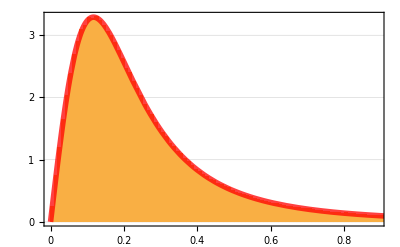

```mathematica
(* let's see if the sampling fnc matches the PDF *)
Clear[a];
a=0.2;
sampleGGXDis:=ArcCos[√((1-#)/(1+(-1+a^2) #))]&[RandomReal[]]
sampleGGXDisX:=ArcSin[a √(#/(1+(-1+a^2) #))]&[RandomReal[]]
Show[
Histogram[ParallelTable[sampleGGXDisX,{i,Range[10^6]}],128,"PDF",PlotTheme->"Business"],
Plot[2π(a^2 Cos[t] Sin[t])/(π (1+(a^2-1) Cos[t]^2)^2),{t,0,π/2},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]]]
]
```

```mathematica
(* Reflect an incoming vector (θ,ϕ) and generate outgoing dirs around that with a GGX distribution *)
(* TODO : LET'S CUT POINT OUTSIDE HEMISPHERE *)

Clear[normal,n,r,tocart,incoming,outgoing];

(* Helper functions *)
r[n_,d_]=(2*(d.n)*n)-d;                                         (*reflect with projections note the -d to reflect on the xy hemiplane*)
tocart[t_,p_] = sp[{1,t,p}] ;                                   (*convert to cartesian*)
newrotax[t_,p_]:=r[{0,0,1},tocart[t,p]];  (* new axe to rotate around to feed RotationTransform *)

(* Arrows *)
incoming[t_,p_]=Style[Arrow[{tocart[t,p],{0,0,0}}],RGBColor[1,1,0.5,1]];
outgoing[t_,p_]=Style[Arrow[{{0,0,0},r[{0,0,1},tocart[t,p]]}],RGBColor[1,0.5,1,1]];
normal = Style[Arrow[{{0,0,0},{0,0,1}}],RGBColor[0.5,1,0.5,0.5]];


(* Parameters *)
Clear[a,nbpts];
a=0.1;
nbpts=2000;
samplethetaggx[x_,a_]:=sampleggxthetaX[x,a]; (* switch here sampling fnc *)

Manipulate[
Show[
Graphics3D@{
hemisphere,
normal,
incoming[t,p],
outgoing[t,p],Style[Point[RotationTransform[{{0,0,1},newrotax[t,p]}][sp/@ParallelTable[{1,samplethetaggx[RandomReal[],a*a],sampleggxphi[RandomReal[]]},{nbpts}]]],RGBColor[1.0,0.5,0.5]]
},
Boxed->False,ImageSize->450
],
{{t,0.8,"Theta θ"},0.0,Pi/2-0.0,0.1},{{p,1.2,"Phi ϕ"},0.0,2 Pi},{{a,0.12,"Roughness"},0.001,1}
]
```

Let’s also keep in mind that sampling naively a Lambert BRDF is fundamentally different than sampling a microfacet BRDF.
On the former we generate a set of uniform directions on the hemisphere and scale them by the BRDF.
On the latter we generate a set of non-uniform directions that match the distribution of the BRDF.

----------------------------------------------------------------------------------------------------------------

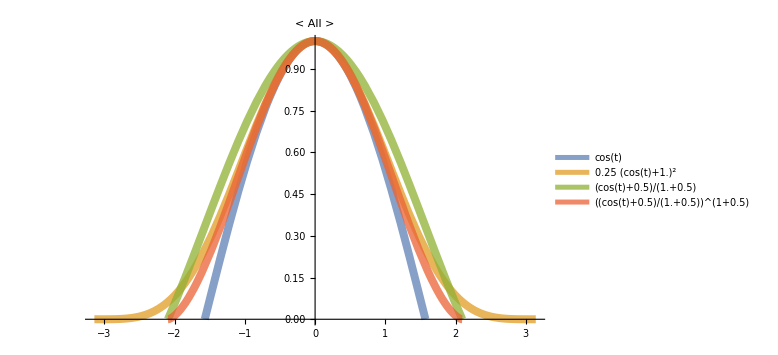

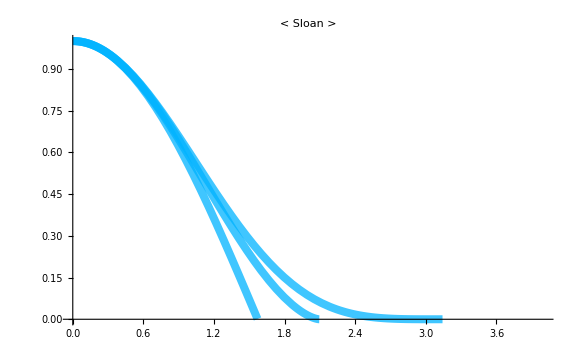

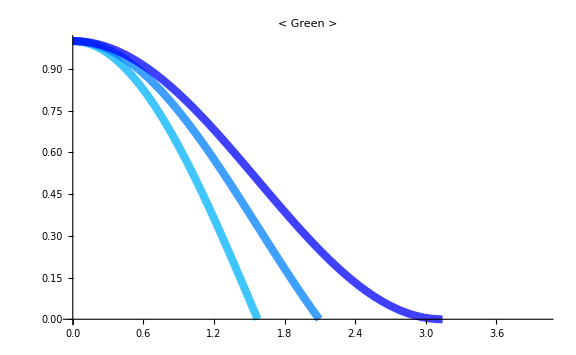

(π+2 π w)/(1+w)

1

```mathematica
(* Wrapped Diffuse *)
Clear[t,w];


With[{w=0.5},Plot[{Cos[t],0.25(Cos[t]+1.0)^2,(Cos[t]+w)/(1.0+w),((Cos[t]+w)/(1.0+w))^(1+w)},{t,-π,π},PlotRange->{{-π,π},{0,1}},PlotLegends->"Expressions",PlotStyle->Directive[Thickness[0.01],Opacity[0.75]],ImageSize->Large,PlotLabel->Style[Row[{"< All >"}],Medium,GrayLevel[0.5]]]]

cos1=With[{w=0.0},Plot[((Cos[t]+w)/(1.0+w))^(1+w),{t,0,π},PlotRange->{{0,4},{0,1}},PlotStyle->Directive[RGBColor[0,0.7,1],Thickness[0.01],Opacity[0.75]]]];
cos2=With[{w=0.5},Plot[((Cos[t]+w)/(1.0+w))^(1+w),{t,0,π},PlotRange->{{0,4},{0,1}},PlotStyle->Directive[RGBColor[0,0.7,1],Thickness[0.01],Opacity[0.75]]]];
cos3=With[{w=1.0},Plot[((Cos[t]+w)/(1.0+w))^(1+w),{t,0,π},PlotRange->{{0,4},{0,1}},PlotStyle->Directive[RGBColor[0,0.7,1],Thickness[0.01],Opacity[0.75]]]];
Show[cos1,cos2,cos3,ImageSize->Large,PlotLabel->Style[Row[{"< Sloan >"}],Medium,GrayLevel[0.5]]]

cos4=With[{w=0.0},Plot[(Cos[t]+w)/(1+w),{t,0,π},PlotRange->{{0,4},{0,1}},PlotStyle->Directive[RGBColor[0,0.7,1],Thickness[0.01],Opacity[0.75]]]];
cos5=With[{w=0.5},Plot[(Cos[t]+w)/(1+w),{t,0,π},PlotRange->{{0,4},{0,1}},PlotStyle->Directive[RGBColor[0,0.5,1],Thickness[0.01],Opacity[0.75]]]];
cos6=With[{w=1.0},Plot[(Cos[t]+w)/(1+w),{t,0,π},PlotRange->{{0,4},{0,1}},PlotStyle->Directive[RGBColor[0,0.0,1],Thickness[0.01],Opacity[0.75]]]];
Show[cos4,cos5,cos6,ImageSize->Large,PlotLabel->Style[Row[{"< Green >"}],Medium,GrayLevel[0.5]]]



∫_0^(2π) ∫_0^(π/2) ((Cos[t]+w)/(1+w))Sin[t]ⅆtⅆp  (* wrapped (Green) cosine weighted hemispherical integral in spherical coords *)
∫_0^(2π) ∫_0^(π/2) (1+w)/(π+2 π w)((Cos[t]+w)/(1+w))Sin[t]ⅆtⅆp  (* wrapped (Green) cosine weighted PDF *)


(*∫_0^(2π) ∫_0^(π/2) 1/π((Cos[t]+w)/(1.0+w))^(1+w)Sin[t]ⅆtⅆp   *)
(*
With[{w=0},Plot[2π(1+w)/(π+2 π w)((Cos[t]+w)/(1+w)),{t,-π/2,π/2},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]]]]
With[{w=0.5},Plot[2π(1+w)/(π+2 π w)((Cos[t]+w)/(1+w)),{t,-π/2,π/2},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]]]]
With[{w=1},Plot[2π(1+w)/(π+2 π w)((Cos[t]+w)/(1+w)),{t,-π/2,π/2},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.75]]]]
*)
```

----------------------------------------------------------------------------------------------------------------

TODOs :: 
- inspect the ‘wrap diffuse’ and the potential distribution tail issue 
from → Monte Carlo Methods and Importance Sampling (https://drive.google.com/drive/folders/1BzOX3hMv0bAqvXrUfZulXZARBcS0k5Vn) 
see at the end the importance sampling pitfaill based on distribution tails .. it’s where with a wrap diffuse we get so much variance !?

----------------------------------------------------------------------------------------------------------------
----------------------------------------------------------------------------------------------------------------

```mathematica
(* MISC: visualize solid angle and the fact that's not related to sphere radius *)
Manipulate[Show[Graphics3D[{Opacity[.75],Sphere[{0,0,0},r]}],RevolutionPlot3D[{r/Tan[ArcCos[1-Ω/(2Pi)]] },{r,0,1}],PlotRange->{{-1,1},{-1,1},{-1,1}},SphericalRegion->True,ImageSize->{480,360},PlotLabel->Style["Area delimited by the cone on the sphere = "<>ToString[NumberForm[Ω*r^2,{5,4}]],"Label",10],ViewVertical->{1,0,0},Boxed->False],{{Ω,1,"solid angle"},0.02,4Pi,0.1,Appearance->"Labeled"},{{r,1,"sphere's radius"},0.1,1,0.1,Appearance->"Labeled"}]
```

```mathematica
(* MISC: visualize the sphere *)
Manipulate[ParametricPlot3D[{Sin[theta] Cos[phi],Sin[theta] Sin[phi],Cos[theta]},{theta,0,t},{phi,0,p},PlotRange->{{-1,1},{-1,1},{-1,1}}],{{t,Pi},0.1,Pi},{{p,Pi},0.1,2 Pi}]
```

```mathematica
Clear[data,rtox];

(* data *)
data=Flatten[Table[{1,theta,phi},{phi,0,2 Pi,Pi/10.},{theta,0,Pi,Pi/10.}],1];

(* cartesian from spherical with buildins *)rtox[sphdata_]:=sphdata/. {r_,theta_,phi_}->CoordinateTransform["Spherical"->"Cartesian",{r,theta,phi}]

ListPointPlot3D[rtox[data],BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Points on sphere by generating a uniform distribution of θ and ϕ directions *)
(* ie. naively multiply a random variate in 0,1 by the full polar angles extents.. 0->π/2 and -π->π *)

(* this is slow like hell *)
Graphics3D@{Sphere[{0,0,0},.98],,Point[CoordinateTransformData["Spherical"->"Cartesian","Mapping",#]&/@Table[{1,RandomReal[{0,Pi/2}],RandomReal[{-Pi,Pi}]},{3000}]]}

(* note clumps on the pole *)
```

-Graphics3D-

```mathematica
color[x_]:=ColorData["Rainbow"][x];
test=Function[{x,y,z},color[Rescale[z,{-0.4,1.05}]]];

Plot3D[Abs@Exp[-(x^2+y^2)],{x,-5,5},{y,-5,5},Mesh->None,PlotPoints->200,ColorFunction->test,Boxed->False,PlotRange->All]
```

-Graphics3D-